```mathematica
sc1=Import["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\A_ex4_final_movies\\The_Italian_Job\\CSV_files\\AB.csv"];
```

```mathematica
srtRegular=Import["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\A_ex4_final_movies\\The_Italian_Job\\CSV_files\\srt_script.csv"];
```

```mathematica
srtFiltered=Import["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\A_ex4_final_movies\\The_Italian_Job\\CSV_files\\filtered.csv"];
```

```mathematica
Grid[sc1,Frame->All];
```

------names characters------

```mathematica
Union[sc1[[;;,2]]]
```

{ALL OF THEM,BULLY,BURLY MAN,BUSBOY,CHARLIE,CHRISTINA GRIEGO,CLASSMATE,COUNTER BABE,CUT BACK TO:,DANYA,DETECTIVE,DRIVER,FADE OUT:,FIRST COP,FURIOUS DRIVER,GUARD,HALF-EAR,HANDSOME ROB,"HE WAS ONE OF M'S BEST STUDENTS",HOMEBOY,JOHN BRIDGER,KAREN,KID,LIVING THE GOOD LIFE ON THE PINK SANDS OF BERMUDA,LYLE,MASHKOV,MOTORCYCLE GUARD,OFFICE,PHILLY STEAK,RECEPTIONIST,RICHARD,SECOND COP,SECURITY GUARD,SEVEN YEAR OLD CHARLIE,SKINNY PETE,Speaker,STELLA,STELLA & CHARLIE,STEVE,THE CREW,UKRAINIAN,VALET,WILL THE REAL NAPSTER PLEASE STAND UP,YEVHEN,YOU'LL NEVER SHUT DOWN THE REAL NAPSTER!}

```mathematica
SortBy[Tally[sc1[[;;,2]]],Last]
```

{{ALL OF THEM,1},{BULLY,1},{BURLY MAN,1},{DRIVER,1},{FADE OUT:,1},{GUARD,1},{"HE WAS ONE OF M'S BEST STUDENTS",1},{KID,1},{LIVING THE GOOD LIFE ON THE PINK SANDS OF BERMUDA,1},{MOTORCYCLE GUARD,1},{OFFICE,1},{Speaker,1},{STELLA & CHARLIE,1},{THE CREW,1},{UKRAINIAN,1},{VALET,1},{WILL THE REAL NAPSTER PLEASE STAND UP,1},{YOU'LL NEVER SHUT DOWN THE REAL NAPSTER!,1},{BUSBOY,2},{CLASSMATE,2},{COUNTER BABE,2},{FIRST COP,2},{SECOND COP,2},{FURIOUS DRIVER,3},{HOMEBOY,3},{SEVEN YEAR OLD CHARLIE,3},{CHRISTINA GRIEGO,4},{DETECTIVE,4},{RECEPTIONIST,4},{CUT BACK TO:,5},{DANYA,5},{KAREN,5},{SECURITY GUARD,6},{PHILLY STEAK,7},{RICHARD,9},{SKINNY PETE,9},{YEVHEN,18},{MASHKOV,21},{JOHN BRIDGER,24},{HALF-EAR,40},{STEVE,54},{HANDSOME ROB,55},{LYLE,70},{STELLA,93},{CHARLIE,167}}

```mathematica
ch = sc1[[;;,2]];
```

```mathematica
e1=Table[ch[[i]]<->ch[[i+1]],{i,1,Length[ch]-1}];
e2=Table[ch[[i]]->ch[[i+1]],{i,1,Length[ch]-1}];
```

```mathematica
v1 = Union[ch];
```

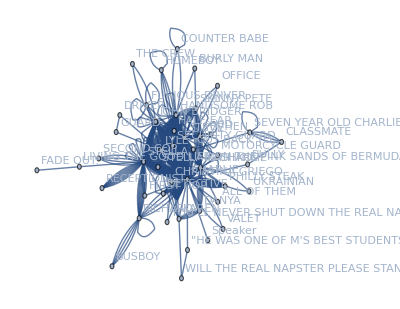

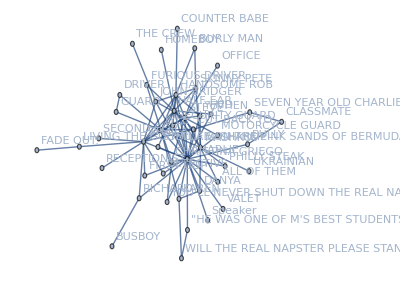

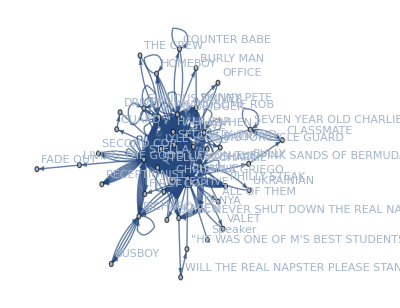

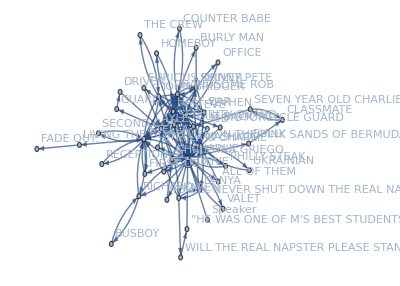

```mathematica
UndirectedWeightedGraph1=Graph[v1,e1,VertexLabels->"Name", ImageSize->Full]
UndirectedNonWeightedGraph2=SimpleGraph[UndirectedWeightedGraph1, ImageSize->Full]
DirectedWeightedGraph3=Graph[v1,e2,VertexLabels->"Name", ImageSize->Full]
DirectedNonWeightedGraph4=SimpleGraph[DirectedWeightedGraph3, ImageSize->Full]
```

THE 4 MAIN CHARACTHERS - italian
VM1our  = what we think
VM1 =  what algo found

```mathematica
VM1our = {"CHARLIE", "STELLA","LYLE" , "STEVE"};
```

```mathematica
PageRankCentrality[UndirectedWeightedGraph1,0.85];
SortBy[Transpose[{VertexList[UndirectedWeightedGraph1],PageRankCentrality[UndirectedWeightedGraph1,0.85]}],Last]
```

{{Speaker,0.00394188},{COUNTER BABE,0.00451983},{VALET,0.00455044},{MOTORCYCLE GUARD,0.0045591},{OFFICE,0.00456777},{KID,0.00459793},{STELLA & CHARLIE,0.00459793},{THE CREW,0.0046075},{FURIOUS DRIVER,0.00461051},{BURLY MAN,0.00474788},{ALL OF THEM,0.00479429},{UKRAINIAN,0.00503815},{YOU'LL NEVER SHUT DOWN THE REAL NAPSTER!,0.00516139},{SECOND COP,0.00573857},{FIRST COP,0.00574581},{HOMEBOY,0.00595752},{BUSBOY,0.00681148},{DRIVER,0.00687732},{GUARD,0.00687732},{"HE WAS ONE OF M'S BEST STUDENTS",0.00715963},{BULLY,0.00722555},{WILL THE REAL NAPSTER PLEASE STAND UP,0.00757116},{FADE OUT:,0.00783649},{RECEPTIONIST,0.0081438},{CHRISTINA GRIEGO,0.00860826},{DETECTIVE,0.00990149},{LIVING THE GOOD LIFE ON THE PINK SANDS OF BERMUDA,0.0105957},{SECURITY GUARD,0.0106631},{CUT BACK TO:,0.011872},{PHILLY STEAK,0.0120969},{DANYA,0.0129839},{KAREN,0.0140586},{SEVEN YEAR OLD CHARLIE,0.0141934},{CLASSMATE,0.0154525},{RICHARD,0.0163678},{SKINNY PETE,0.0173921},{YEVHEN,0.0195596},{JOHN BRIDGER,0.0314793},{MASHKOV,0.0381076},{HALF-EAR,0.0555709},{HANDSOME ROB,0.0739817},{STEVE,0.0755186},{LYLE,0.080381},{STELLA,0.125921},{CHARLIE,0.209055}}

```mathematica
(*{"STEVE",0.07551859691827262},{"LYLE",0.08038103017405371},{"STELLA",0.12592098161421025},{"CHARLIE",0.20905518733434855}*)
VM1 = {"CHARLIE", "STELLA","LYLE" , "STEVE"};
```

#### q 5-8

q 6)

```mathematica
r=Drop[srtRegular[[;;,4]],4];
v=Union[r];
```

```mathematica
FromL2GD1[v,l_]:=Module[{i},
Graph[v,Table[l[[i-1]]->  l[[i]],{i,2,Length[l]}],VertexLabels->All,GraphLayout->"CircularEmbedding"]
];
```

```mathematica
γ=Table[FromL2GD1[v,Take[r,{1,i}]],{i,2,Length[r]-1}];
Length[γ]
```

1604

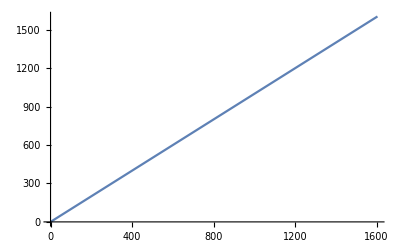

```mathematica
Ce=Table[EdgeCount[γ[[i]]],{i,1,Length[γ]}];
ListLinePlot[Ce]
```

TextWords::arg1: String or ContentObject expected at position 1.

Part::partw: Part 1610 of {{Hello,sweetie},{Daddy},{It's,early},{Yeah,I,know},{I,just,wanted,to,let,you,know,I'm,sending,you,«1»},{Mmm,Does,it,smell,nice},{No},{but,it's,sparkly},{Does,it,have,a,receipt},{I'm,sending,it,to,you,from,the,store},«1599»} does not exist.

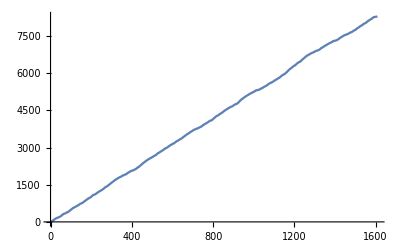

```mathematica
W=Table[TextWords[srtRegular[[i,3]]],{i,2,Length[srtRegular]}];
Cw=Accumulate[Table[Length[W[[i]]],{i,2,Length[srtRegular]}]];
ListLinePlot[Cw]
```

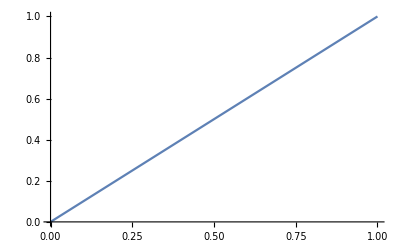

```mathematica
NCe=Table[{(i-1)/(Length[Ce]-1),(Ce[[i]]-1)/(Ce[[-1]]-1)},{i,1,Length[Ce]}];
ListLinePlot[NCe]
```

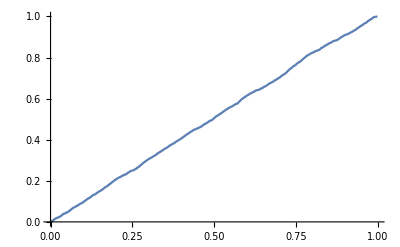

```mathematica
NCw=Table[{(i-1)/(Length[Cw]-1),(Cw[[i]]-1)/(Cw[[-1]]-1)},{i,1,Length[Cw]-1}];
ListLinePlot[NCw]
```

```mathematica
NormalzLC[C1_]:=If[C1[[1]]==0,
C1/C1[[-1]](* The input is a clock C1. The output is normalize cock *)
,Join[{0},C1/C1[[-1]]]
];
```

```mathematica
MDiagram[C1_,C2_]:=Module[{nc1,nc2,i},(* The input is two clocks and the output is M diagram of the two clocks*)
nc1=NormalzLC[C1];
nc2=NormalzLC[C2];
Table[{(i-1)/(Length[nc1]-1),nc1[[i]]-nc2[[i]]},{i,1,Min[Length[nc1],Length[nc2]]}]
]
```

{{0,0},{1/1604,6689/13301972},{1/802,5887/6650986},{3/1604,15255/13301972},{1/401,1476/3325493},{5/1604,6177/13301972},{3/802,6433/6650986},1591,{799/802,-11245/6650986},{1599/1604,-17405/13301972},{400/401,-2679/3325493},{1601/1604,-5631/13301972},{801/802,529/6650986},{1603/1604,6143/13301972},{1,8/8293}}
 |  |  |  |

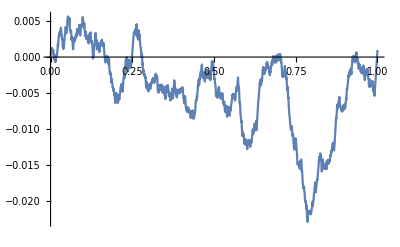

```mathematica
MCeCw=MDiagram[Ce,Cw]
ListLinePlot[MCeCw]
```

#### more about q6

```mathematica
fps=5.88578
movietimeSeconds=143.15*60
totalframes =fps*movietimeSeconds
getFram[start_,end_]:=Module[{list,interval},
list = {start,end};
interval=3600 FromDMS[ToExpression[StringSplit[#,":"]]]&/@list;
{Ceiling[fps*(interval[[1]])],Floor[fps*(interval[[2]])]}
];
TransforminTheSrt[srtscript_]:=Module[{l},(* the input is srt-script the output is a table contain a list for each srt-script line. the list have 
 1. String of the time srt apper on the screen
 2. String of the time the srt disappear form the screen
 3. frame number for the srt to apper on the screen
 4. frame number for the srt to disappear form the screen
  *)
l={};
For[i=2,i≤Length[srtscript],i++,
apper=srtscript[[i]][[1]];
disappear = srtscript[[i]][[2]];
whatissaid = srtscript[[i]][[3]];
time=getFram[apper,disappear];
AppendTo[l,{apper,disappear,time[[1]],time[[2]],whatissaid}];
];
l
];
GetCriticalPoint[MD_,n_,llrw_]:=Module[{p,p1,p2,i,ln,fig1,table1,table2},
ln=Length[MD];
p1=Sort[Flatten[ParallelTable[Ordering[Take[MD[[;;,2]],{ (i-1)Floor[ln/n]+1,(i)Floor[ln/n]}]][[{1,-1}]]+ (i-1)Floor[ln/n]-1,{i,1,n}]]];
p2=Sort[Flatten[ParallelTable[Ordering[Take[MD[[;;,2]],{ (i-1)Floor[ln/(n+1)]+1,(i)Floor[ln/(n+1)]}]][[{1,-1}]]+ (i-1)Floor[ln/(n+1)]-1,{i,1,n+1}]]];
p=Intersection[p1,p2];
fig1=ListLinePlot[MD,Epilog->{Red,PointSize[0.02],Point[MD[[p+1]]]}];
table1=Join[{{"#Resphonse","Normaliz","When","What"}},Table[{p[[i]],N[p[[i]]/Length[MD]],llrw[[;;,1]][[p[[i]]]],llrw[[;;,-1]][[p[[i]]]]},{i,1,Length[p]}]];
table2=TextGrid[table1,Frame->All];
{fig1,table2}
];
```

5.88578

8589.

50553.

```mathematica
llrw=TransforminTheSrt[srtRegular]
```

ToExpression::sntx: Invalid syntax in or before "45,928".
                                                    ^

FromDMS::dms: {0,2,$Failed} cannot be interpreted as a degree-minute-second list specification.

ToExpression::sntx: Invalid syntax in or before "47,930".
                                                    ^

FromDMS::dms: {0,2,$Failed} cannot be interpreted as a degree-minute-second list specification.

ToExpression::sntx: Invalid syntax in or before "48,014".
                                                    ^

General::stop: Further output of ToExpression::sntx
     will be suppressed during this calculation.

FromDMS::dms: {0,2,$Failed} cannot be interpreted as a degree-minute-second list specification.

General::stop: Further output of FromDMS::dms will be suppressed during this calculation.

{{00:02:45,928,00:02:47,930
,Ceiling[21188.8 FromDMS[{0,2,$Failed}]],Floor[21188.8 FromDMS[{0,2,$Failed}]],Hello, sweetie.},1607,{01:48:26,602,01:48:27,561
,Ceiling[21188.8 FromDMS[{1}]],Floor[21188.8 FromDMS[{1,48,$Failed}]],Away...}}
 |  |  |  |

#### see in the srt_script where are the critical points

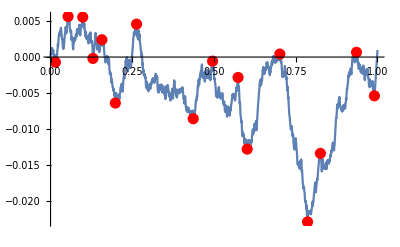
{-Graphics-,#Resphonse | Normaliz | When | What
24 | 0.0149533 | 00:03:43,653 | I'm on a cell phone, darling.
86 | 0.0535826 | 00:06:00,873 | If you don't mind.
158 | 0.0984424 | 00:18:13,397 | In gold.
208 | 0.129595 | 00:20:01,422 | Don't get to be my age with nothing but this, Charlie.
252 | 0.157009 | 00:25:20,283 | who to call first.
318 | 0.198131 | 00:27:54,562 | Look, I'm sorry, all right?
422 | 0.262928 | 00:33:25,935 | Let's go.
700 | 0.436137 | 00:48:16,158 | and the cable modem on the computer in the office.
795 | 0.495327 | 00:53:08,492 | Becky, huh?
920 | 0.573209 | 01:00:34,438 | What are those?
965 | 0.601246 | 01:02:23,422 | And what did Italy need gold for?
1125 | 0.700935 | 01:11:20,835 | Can't remember.
1261 | 0.78567 | 01:18:07,992 | We can't have a shoot-out with armed guards. We'd lose.
1324 | 0.824922 | 01:21:55,511 | What's wrong?
1501 | 0.935202 | 01:41:42,698 | in there, right? Mini Coopers?
1589 | 0.990031 | 01:47:43,184 | Is the root of all evil today}

```mathematica
GetCriticalPoint[MCeCw,13,llrw]
```

### q7)

```mathematica
rFilt=Drop[srtFiltered[[;;,4]],4];
vFilt=Union[rFilt];
```

```mathematica
FromL2GD1[v,l_]:=Module[{i},
Graph[v,Table[l[[i-1]]->  l[[i]],{i,2,Length[l]}],VertexLabels->All,GraphLayout->"CircularEmbedding"]
];
```

```mathematica
γ=Table[FromL2GD1[vFilt,Take[rFilt,{1,i}]],{i,2,Length[rFilt]-1}];
Length[γ]
```

1604

```mathematica
CeH=Table[EdgeCount[γ[[i]]],{i,1,Length[γ]}];
ListLinePlot[CeH]
```

-Graphics-

Part::partw: Part 1610 of {{},{},{},{},{},{},{},{},{},{},«1599»} does not exist.

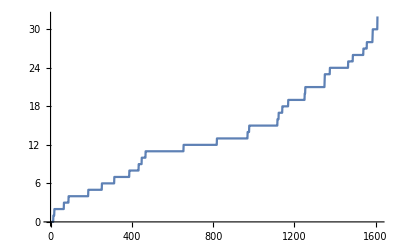

```mathematica
WH=Table[TextWords[srtFiltered[[i,3]]],{i,2,Length[srtFiltered]}];
CwH=Accumulate[Table[Length[WH[[i]]],{i,2,Length[srtFiltered]}]];
ListLinePlot[CwH]
```